```mathematica
Zip[a_,b_]:=Module[{i, output},
output={};
For[i=1,i≤Length[a],i++,
AppendTo[output,{a[[i]],b[[i]]}];
];
Return[output];
];
```

```mathematica
roots[f_,x_,sdom_:True]:=Module[{i,rawSol,root,output},
rawSol=Solve[f==0&&sdom,x,Reals];
root={};
output={};
For[i=1,i≤Length[rawSol],i++,
If[rawSol[[i,1,2,0]]==Root,
AppendTo[root,N[rawSol[[i]],2]];
Continue[];
];
AppendTo[root,rawSol[[i]]];
];
If[Or[root=={{}},root=={}],
Return[{}],
For[i=1,i≤Length[root],i++,
AppendTo[output, {root[[i,1,2]],0}];
];
Return[output]
];
];
```

```mathematica
approximateRoots[solutions_]:=Module[{i, output},
output={};
For[i=1,i≤Length[solutions],i++,
If[solutions[[i,1,2,0]]==Root,
AppendTo[output, N[solutions[[i]],2]];
Continue[];
];
AppendTo[output, solutions[[i]]];
];
Return[output];
];
```

```mathematica
turningPoints[f_,x_,sdom_:True]:=Module[{solveResult,skippedIfStatment},
skippedIfStatment=True;
If[D[f,x]==0,
skippedIfStatment=False;
solveResult={{}};
];
If[skippedIfStatment,
solveResult=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]];
];
If[Or[solveResult=={{}},solveResult=={}],
Return[{}]
,
Return[Zip[solveResult[[All,1,2]],f/.x->solveResult[[All,1,2]]]]
];
Print["The answer is liable to contain errors"];
Return[{}]
];
```

```mathematica
maximumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])<0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
```

```mathematica
minimumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])>0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
```

```mathematica
stationaryPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[{}];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=False;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=True;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
```

```mathematica
movingPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[Zip[secondDSolutions[[All,1,2]],f/.x->secondDSolutions[[All,1,2]]]];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=True;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=False;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
```

```mathematica
concaviteAtPointAsInteger[f_,x_,p_]:=Module[{secondD},
secondD=D[f,{x,2}];
If[(secondD/.x->p)≤0,
Return[1]
,
Return[-1]
];
Return["Error"];
];
```

```mathematica
yIntercepts[f_,x_,sdom_:True]:=Module[{},
If[(f&&sdom/.x->0)==False,
Return[{}];
];
Return[{{0,(f&&sdom/.x->0)}}];
];
```

```mathematica
evalulateValue[val_]:=val
```

```mathematica
plotColors[n_]:=ColorData[97,"ColorList"][[Mod[n,15]]]
```

```mathematica
plotinator[f_,dom_,showObliqueAsymptotes_:False]:=Module[{i,j,keyPoints,plot,absoluteRange,epilogPoints,epologTextOffset,epilogs,hAsymptotes,vAsymptotes,oAsymptotes,asymptotes,solveDomain,plotEquasions,oAsymptoteHolder,plotStyle,pointObjects,numberOfEquasions},
keyPoints={};
plot=0;
absoluteRange=0;
epilogPoints=0;
epologTextOffset=0;
epilogs={};
solveDomain=dom[[2]]≤dom[[1]]≤dom[[3]];
plotEquasions={f};
oAsymptoteHolder={};
plotStyle={};
pointObjects={};
numberOfEquasions=0;

If[(f)[[0]]==List,
plotEquasions=f;
];

For[i=1,i≤Length[plotEquasions],i++,
AppendTo[plotStyle,{plotColors[i]}]
];
For[i=1,i≤Length[plotEquasions],i++,
keyPoints=Join[keyPoints,movingPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,stationaryPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,turningPoints[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,roots[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,yIntercepts[plotEquasions[[i]],dom[[1]],solveDomain]];
];
keyPoints=DeleteDuplicates[keyPoints];

plot=Plot[f,dom];
absoluteRange=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]];
For[j=1,j≤Length[plotEquasions],j++,
For[i=1,i≤Length[keyPoints],i++,
epologTextOffset=1/10*absoluteRange*concaviteAtPointAsInteger[plotEquasions[[j]],dom[[1]],keyPoints[[i,1]]];
AppendTo[epilogs,Text[keyPoints[[i]],{keyPoints[[i,1]],keyPoints[[i,2]]+epologTextOffset}]];
];
];

asymptotes={};
For[j=1,j≤Length[plotEquasions],j++,
hAsymptotes=horizontalAsymptotes[plotEquasions[[j]],dom[[1]]];
vAsymptotes=verticleAsymptotes[plotEquasions[[j]],dom[[1]]];
oAsymptotes=obliqueAsymptote[plotEquasions[[j]],dom[[1]]];
For[i=1,i≤Length[hAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{dom[[2]],hAsymptotes[[i]]},{dom[[3]],hAsymptotes[[i]]}}],y==hAsymptotes[[i]]]];
];
For[i=1,i≤Length[vAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{vAsymptotes[[i]],PlotRange[plot][[2,1]]},{vAsymptotes[[i]],PlotRange[plot][[2,2]]}}],x==vAsymptotes[[i]]]];
];
For[i=1,i≤Length[oAsymptotes],i++,
AppendTo[oAsymptoteHolder,oAsymptotes[[i]]];
];
];

If[showObliqueAsymptotes,
Print["showing oblique asymptotes"];
oAsymptoteHolder=DeleteDuplicates[oAsymptoteHolder];
For[i=1,i≤Length[oAsymptoteHolder],i++,
AppendTo[plotEquasions,oAsymptoteHolder[[i]]];
];

For[i=1,i≤(Length[oAsymptoteHolder]),i++,
AppendTo[plotStyle,{Red,Dashed}];
];
];

For[i=1,i≤Length[keyPoints],i++,
AppendTo[pointObjects,Tooltip[Point[keyPoints[[i]]],{keyPoints[[i,1]],keyPoints[[i,2]]}]];
];

plot=Plot[plotEquasions,dom,Epilog->{PointSize[Large],pointObjects,(*epilogs,*)Directive[Red,Dashed],asymptotes},PlotStyle->plotStyle,PlotLegends->"Expressions"];
Return[plot];
];
```

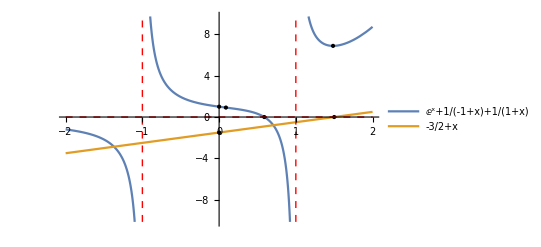

```mathematica
plotinator[{ⅇ^x+1/(x-1)+1/(x+1),x-3/2},{x,-2,2}]
```

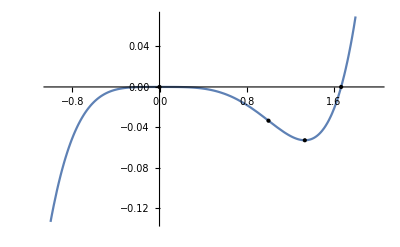

```mathematica
plotinator[-x^4/12+x^5/20,{x,-1,2}]
```

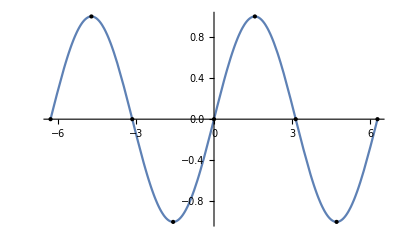

```mathematica
plotinator[Sin[x],{x,-2π,2π}]
```

```mathematica
ClearAll[obliqueAsymptote]
```

```mathematica
obliqueAsymptote[f_,x_]:=Module[{i,expandedForm,temp,output,hasOAsymptote},
expandedForm=Expand[f];
If[expandedForm[[0]]==Plus,
temp={};
output={};
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->-∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
output=DeleteDuplicates[output];
Return[output];
];
Return[{}];
];
```

```mathematica
valueOfInequality[inequ_,x_]:=Module[{},
If[inequ[[2]]==x,Return[inequ[[1]]]];
If[inequ[[1]]==x,Return[inequ[[2]]]];
]
```

```mathematica
verticleAsymptotes[f_,x_]:=Module[{i,j,dom,asymptotes,output},
dom=FunctionDomain[f,x];
asymptotes={};
output={};
For[i=1,i≤Length[dom],i++,
If[dom[[i,0]]==Less,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Greater,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Inequality,
For[j=1,j≤Length[dom[[i]]]-2,j=j+2,
AppendTo[asymptotes,valueOfInequality[dom[[i,j;;j+2]],x]];
];
];
];
asymptotes=DeleteDuplicates[asymptotes];
For[i=1,i≤Length[asymptotes],i++,
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
];
output=DeleteDuplicates[output];
Return[output];
];
```

```mathematica
horizontalAsymptotes[f_,x_]:=Module[{output,val},
output={};
val=0;
val=Limit[f,x->∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
val=Limit[f,x->-∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
output=DeleteDuplicates[output];
Return[output];
];
```